```mathematica
a = 2 Power[,2](Power[,2] Power[,2] - Power[,2])-//Expand
b = Power[a,2]+Power[,2]-8 Power[,2] Power[,2]  - 4 Power[,2] Power[,2] Power[,2]//ExpandAll//Evaluate//Simplify
expr = Collect[Power[x,4]+4a Power[x,2]+16  I   x+4 b//ExpandAll//Simplify,x]
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

-V+2 m^2 S^2 η^2-2 η^2 Π^2

V^2+W^2-4 m^2 U^2 η^2+4 m^4 S^4 η^4-8 m^2 S^2 η^4 Π^2+4 η^4 Π^4-4 V η^2 (m^2 S^2+Π^2)

4 V^2+4 W^2+x^4-16 m^2 U^2 η^2+16 m^4 S^4 η^4+16 ⅈ W x η Π-32 m^2 S^2 η^4 Π^2+16 η^4 Π^4-16 V η^2 (m^2 S^2+Π^2)+x^2 (-4 V+8 m^2 S^2 η^2-8 η^2 Π^2)

{{x→0},{x→0},{x→0},{x→0}}

```mathematica
Solve[(expr==0/.{->-I }),x]//Expand//Simplify
```

{{x→1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3))-√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(12 √3 V η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)))))},{x→1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(12 √3 V η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)))))},{x→-1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(12 √3 V η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)))))},{x→1/(√3)(-√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)-(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(12 √3 V η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)+(54 V^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3-36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2)))+√(-(V^2+16 m^4 S^4 η^4+16 η^4 Π^4-8 V η^2 (2 m^2 S^2+Π^2)-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+(-54 V^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3+36 η^2 (V+2 η^2 (-m^2 S^2+Π^2)) (-m^4 S^4 η^2+Π^2 (V-η^2 Π^2)+m^2 (U^2+S^2 (V+2 η^2 Π^2))))^2))^(1/3)))))}}

```mathematica
Solve[(expr==0/.{->-I }/.{-> }),x]//Expand//Simplify
```

{{x→1/(√3)(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))-√(4 V+(-V^2+12 m^2 U^2 η^2+24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))-(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)-(12 √3 m S V η)/(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)))))},{x→1/(√3)(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+√(4 V+(-V^2+12 m^2 U^2 η^2+24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))-(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)-(12 √3 m S V η)/(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)))))},{x→-1/(√3)(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+√(4 V+(-V^2+12 m^2 U^2 η^2+24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))-(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)+(12 √3 m S V η)/(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)))))},{x→1/(√3)(-√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+√(4 V+(-V^2+12 m^2 U^2 η^2+24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))-(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)+(12 √3 m S V η)/(√(2 V+(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)/((-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3))+(-V^3-36 m^2 U^2 V η^2-18 m^2 S^2 V^2 η^2+√(-(V^2-12 m^2 U^2 η^2-24 m^2 S^2 V η^2)^3+V^2 (V^2+36 m^2 U^2 η^2+18 m^2 S^2 V η^2)^2))^(1/3)))))}}

```mathematica
Solve[(expr==0/.{->0}/.{->-I }/.{-> }),x]//Expand//Simplify
```

{{x→1/(√3)(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))-√(4 V-(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))-(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)-(12 √3 m S V η)/(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)))))},{x→1/(√3)(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+√(4 V-(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))-(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)-(12 √3 m S V η)/(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)))))},{x→-1/(√3)(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+√(4 V-(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))-(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)+(12 √3 m S V η)/(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)))))},{x→1/(√3)(-√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+√(4 V-(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))-(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)+(12 √3 m S V η)/(√(2 V+(V (V-24 m^2 S^2 η^2))/((-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3))+(-V^3-18 m^2 S^2 V^2 η^2+6 √3 √(m^2 S^2 V^3 η^2 (V^2-13 m^2 S^2 V η^2+128 m^4 S^4 η^4)))^(1/3)))))}}

```mathematica
Solve[(expr==0/.{->0}/.{->-I }/.{->0}),x]//Expand//Simplify
```

{{x→-2 ⅈ m S η},{x→2 ⅈ m S η},{x→-2 √(V-m^2 S^2 η^2)},{x→2 √(V-m^2 S^2 η^2)}}

```mathematica
Solve[(expr==0/.{->0}/.{->-I }/.{->0}),x]//Expand//Simplify
```

{{x→2 η Π},{x→2 η Π},{x→2 (√V-η Π)},{x→-2 (√V+η Π)}}

```mathematica
Solve[(expr==0/.{->0}/.{->-I }/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→0},{x→0},{x→-2 √V},{x→2 √V}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 ⅈ m S η},{x→-2 ⅈ m S η},{x→2 ⅈ m S η},{x→2 ⅈ m S η}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 √m √U √η},{x→-2 ⅈ √m √U √η},{x→2 ⅈ √m √U √η},{x→2 √m √U √η}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→(-1-ⅈ) √W},{x→(1+ⅈ) √W},{x→(1-ⅈ) √W},{x→(-1+ⅈ) √W}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 η Π},{x→-2 η Π},{x→2 η Π},{x→2 η Π}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √V},{x→-√2 √V},{x→√2 √V},{x→√2 √V}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 ⅈ √m √η √(U+m S^2 η)},{x→2 ⅈ √m √η √(U+m S^2 η)},{x→-2 √(-m η (-U+m S^2 η))},{x→2 √(-m η (-U+m S^2 η))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√(-2 ⅈ W-4 m^2 S^2 η^2)},{x→√(-2 ⅈ W-4 m^2 S^2 η^2)},{x→-√(2 ⅈ W-4 m^2 S^2 η^2)},{x→√(2 ⅈ W-4 m^2 S^2 η^2)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 √(-η^2 (m^2 S^2-Π^2))},{x→-2 √(-η^2 (m^2 S^2-Π^2))},{x→2 √(-η^2 (m^2 S^2-Π^2))},{x→2 √(-η^2 (m^2 S^2-Π^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-2 m^2 S^2 η^2)},{x→-√2 √(V-2 m^2 S^2 η^2)},{x→√2 √(V-2 m^2 S^2 η^2)},{x→√2 √(V-2 m^2 S^2 η^2)}}

```mathematica
Solve[(expr==0/.{->0}/.{->-I }/.{->0}),x]//Expand//Simplify
```

{{x→-2 ⅈ m S η},{x→2 ⅈ m S η},{x→-2 √(V-m^2 S^2 η^2)},{x→2 √(V-m^2 S^2 η^2)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 (-W^2+4 m^2 U^2 η^2)^(1/4)},{x→-ⅈ √2 (-W^2+4 m^2 U^2 η^2)^(1/4)},{x→ⅈ √2 (-W^2+4 m^2 U^2 η^2)^(1/4)},{x→√2 (-W^2+4 m^2 U^2 η^2)^(1/4)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 √(η (-m U+η Π^2))},{x→2 √(η (-m U+η Π^2))},{x→-2 √(η (m U+η Π^2))},{x→2 √(η (m U+η Π^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-2 m U η)},{x→√2 √(V-2 m U η)},{x→-√2 √(V+2 m U η)},{x→√2 √(V+2 m U η)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→(-1+ⅈ) √W+2 η Π},{x→(1+ⅈ) √W-2 η Π},{x→(-1-ⅈ) √W-2 η Π},{x→(1-ⅈ) √W+2 η Π}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-ⅈ W)},{x→√2 √(V-ⅈ W)},{x→-√2 √(V+ⅈ W)},{x→√2 √(V+ⅈ W)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √V-2 η Π},{x→√2 √V-2 η Π},{x→-√2 √V+2 η Π},{x→√2 √V+2 η Π}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(-2 m^2 S^2 η^2-√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(-2 m^2 S^2 η^2-√(-W^2+4 m^2 U^2 η^2))},{x→-√2 √(-2 m^2 S^2 η^2+√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(-2 m^2 S^2 η^2+√(-W^2+4 m^2 U^2 η^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-2 √(-η (m U+m^2 S^2 η-η Π^2))},{x→2 √(-η (m U+m^2 S^2 η-η Π^2))},{x→-2 √(η (m U-m^2 S^2 η+η Π^2))},{x→2 √(η (m U-m^2 S^2 η+η Π^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-2 m η (U+m S^2 η))},{x→√2 √(V-2 m η (U+m S^2 η))},{x→-√2 √(V+2 m η (U-m S^2 η))},{x→√2 √(V+2 m η (U-m S^2 η))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)))-1/2 √(-32/3 η^2 (m^2 S^2-Π^2)-(4 (3 W^2+16 η^4 (-m^2 S^2+Π^2)^2))/(3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))-4/3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)-(16 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))))},{x→1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)))+1/2 √(-32/3 η^2 (m^2 S^2-Π^2)-(4 (3 W^2+16 η^4 (-m^2 S^2+Π^2)^2))/(3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))-4/3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)-(16 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))))},{x→-1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)))-1/2 √(-32/3 η^2 (m^2 S^2-Π^2)-(4 (3 W^2+16 η^4 (-m^2 S^2+Π^2)^2))/(3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))-4/3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)+(16 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))))},{x→-1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)))+1/2 √(-32/3 η^2 (m^2 S^2-Π^2)-(4 (3 W^2+16 η^4 (-m^2 S^2+Π^2)^2))/(3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))-4/3 (-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3)+(16 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 η^4 (-m^2 S^2+Π^2)^2)/((-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))+(-64 m^6 S^6 η^6-36 W^2 η^2 Π^2+192 m^4 S^4 η^6 Π^2+64 η^6 Π^6-6 m^2 S^2 η^2 (3 W^2+32 η^4 Π^4)+3 √3 √(-W^2 (W^4+256 η^8 Π^2 (-m^2 S^2+Π^2)^3+4 W^2 η^4 (m^4 S^4-20 m^2 S^2 Π^2-8 Π^4))))^(1/3))))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-ⅈ W-2 m^2 S^2 η^2)},{x→√2 √(V-ⅈ W-2 m^2 S^2 η^2)},{x→-√2 √(V+ⅈ W-2 m^2 S^2 η^2)},{x→√2 √(V+ⅈ W-2 m^2 S^2 η^2)}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-2 √2 √V η Π+2 η^2 (-m^2 S^2+Π^2))},{x→√2 √(V-2 √2 √V η Π+2 η^2 (-m^2 S^2+Π^2))},{x→-√2 √(V+2 √2 √V η Π+2 η^2 (-m^2 S^2+Π^2))},{x→√2 √(V+2 √2 √V η Π+2 η^2 (-m^2 S^2+Π^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→1/2 √((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-1/2 √((32 η^2 Π^2)/3+(-12 W^2+48 m^2 U^2 η^2-64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3)-(32 ⅈ W η Π)/(√((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))))},{x→1/2 √((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+1/2 √((32 η^2 Π^2)/3+(-12 W^2+48 m^2 U^2 η^2-64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3)-(32 ⅈ W η Π)/(√((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))))},{x→-1/2 √((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-1/2 √((32 η^2 Π^2)/3+(-12 W^2+48 m^2 U^2 η^2-64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3)+(32 ⅈ W η Π)/(√((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))))},{x→-1/2 √((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+1/2 √((32 η^2 Π^2)/3+(-12 W^2+48 m^2 U^2 η^2-64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))-4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3)+(32 ⅈ W η Π)/(√((16 η^2 Π^2)/3+(12 W^2-48 m^2 U^2 η^2+64 η^4 Π^4)/(3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))+4/3 (-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+64 η^6 Π^6+3 √3 √(-W^6+64 m^4 U^4 η^6 (m^2 U^2-η^2 Π^4)+4 W^4 (3 m^2 U^2 η^2+8 η^4 Π^4)-16 W^2 (3 m^4 U^4 η^4-20 m^2 U^2 η^6 Π^4+16 η^8 Π^8)))^(1/3))))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(V-√(-W^2+4 m^2 U^2 η^2))},{x→-√2 √(V+√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(V+√(-W^2+4 m^2 U^2 η^2))}}

```mathematica
Solve[(expr==0/.{->0}/.{->0}),x]//Expand//Simplify
```

{{x→-√(2 V+4 η^2 Π^2-4 √(η^2 (m^2 U^2+2 V Π^2)))},{x→√(2 V+4 η^2 Π^2-4 √(η^2 (m^2 U^2+2 V Π^2)))},{x→-√(2 V+4 (η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))},{x→√(2 V+4 (η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))}}

```mathematica
Solve[(expr==0/.{->0}),x]//Expand//Simplify
```

{{x→1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3))-√(-8 η^2 (m^2 S^2-Π^2)-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)))))},{x→1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3))+√(-8 η^2 (m^2 S^2-Π^2)-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)))))},{x→-1/(√3)(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3))+√(-8 η^2 (m^2 S^2-Π^2)-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)))))},{x→1/(√3)(-√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3))+√(-8 η^2 (m^2 S^2-Π^2)-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)-(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(4 η^2 (-m^2 S^2+Π^2)+(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))/(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)+(-18 m^2 S^2 W^2 η^2+72 m^4 S^2 U^2 η^4-64 m^6 S^6 η^6-36 W^2 η^2 Π^2-72 m^2 U^2 η^4 Π^2+192 m^4 S^4 η^6 Π^2-192 m^2 S^2 η^6 Π^4+64 η^6 Π^6+√(-(3 W^2+16 m^4 S^4 η^4+16 η^4 Π^4-4 m^2 (3 U^2 η^2+8 S^2 η^4 Π^2))^3+4 η^4 (32 m^6 S^6 η^4+18 W^2 Π^2-32 η^4 Π^6-12 m^4 (3 S^2 U^2 η^2+8 S^4 η^4 Π^2)+m^2 (36 U^2 η^2 Π^2+S^2 (9 W^2+96 η^4 Π^4)))^2))^(1/3)))))}}

```mathematica
Solve[(expr==0/.{->0}),x]//Expand//Simplify
```

{{x→-√2 √(V-2 m^2 S^2 η^2-√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(V-2 m^2 S^2 η^2-√(-W^2+4 m^2 U^2 η^2))},{x→-√2 √(V-2 m^2 S^2 η^2+√(-W^2+4 m^2 U^2 η^2))},{x→√2 √(V-2 m^2 S^2 η^2+√(-W^2+4 m^2 U^2 η^2))}}

```mathematica
Solve[(expr==0/.{->0}),x]//Expand//Simplify
```

{{x→-√(2 V-4 (m^2 S^2 η^2-η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))},{x→√(2 V-4 (m^2 S^2 η^2-η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))},{x→-√(2 V+4 (-m^2 S^2 η^2+η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))},{x→√(2 V+4 (-m^2 S^2 η^2+η^2 Π^2+√(η^2 (m^2 U^2+2 V Π^2))))}}

```mathematica
Solve[(expr==0/.{->0}),x]//Expand//Simplify
```

{{x→1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3))-√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)))))},{x→1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)))))},{x→-1/(√3)(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)))))},{x→1/(√3)(-√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3))+√(4 (V+2 η^2 (-m^2 S^2+Π^2))-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 (-m^2 S^2+Π^2))+(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))/(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 (-m^2 S^2+Π^2))^3+9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2))+√(-(4 V^2+3 W^2+16 η^4 (-m^2 S^2+Π^2)^2-8 V η^2 (2 m^2 S^2+Π^2))^3+(54 W^2 η^2 Π^2+(V+2 η^2 (-m^2 S^2+Π^2))^3-9 (V+2 η^2 (-m^2 S^2+Π^2)) (V^2+W^2+4 η^4 (-m^2 S^2+Π^2)^2-4 V η^2 (m^2 S^2+Π^2)))^2))^(1/3)))))}}

```mathematica
Solve[(expr==0/.{->0}),x]//Expand//FullSimplify
```

{{x→1/(√3)(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3))-√(4 (V+2 η^2 Π^2)+(-4 V^2-3 W^2+12 m^2 U^2 η^2+8 V η^2 Π^2-16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)))))},{x→1/(√3)(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3))+√(4 (V+2 η^2 Π^2)+(-4 V^2-3 W^2+12 m^2 U^2 η^2+8 V η^2 Π^2-16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)))))},{x→-1/(√3)(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3))+√(4 (V+2 η^2 Π^2)+(-4 V^2-3 W^2+12 m^2 U^2 η^2+8 V η^2 Π^2-16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)))))},{x→1/(√3)(-√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3))+√(4 (V+2 η^2 Π^2)+(-4 V^2-3 W^2+12 m^2 U^2 η^2+8 V η^2 Π^2-16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)-(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(12 ⅈ √3 W η Π)/(√(2 (V+2 η^2 Π^2)+(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)/(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)+(-54 W^2 η^2 Π^2-(V+2 η^2 Π^2)^3+9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4)+√(-(4 V^2+3 W^2-12 m^2 U^2 η^2-8 V η^2 Π^2+16 η^4 Π^4)^3+(54 W^2 η^2 Π^2+(V+2 η^2 Π^2)^3-9 (V+2 η^2 Π^2) (V^2+W^2-4 m^2 U^2 η^2-4 V η^2 Π^2+4 η^4 Π^4))^2))^(1/3)))))}}

```mathematica
res = Solve[expr==0,x]//Expand//Simplify
```

```mathematica
Solve[x^4 + A x^2 + I B x + c==0,x]//ExpandAll//Evaluate//FullSimplify
```

{{x→1/12 (√6 √((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)))-6 √(-(4 A)/3-A^2/(3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-(4 c)/((A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-1/3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)-(2 ⅈ √6 B)/(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))))))},{x→1/12 (√6 √((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)))+6 √(-(4 A)/3-A^2/(3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-(4 c)/((A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-1/3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)-(2 ⅈ √6 B)/(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))))))},{x→-(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))))/(2 √6)-1/2 √(-(4 A)/3-A^2/(3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-(4 c)/((A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-1/3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)+(2 ⅈ √6 B)/(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)))))},{x→-(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))))/(2 √6)+1/2 √(-(4 A)/3-A^2/(3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-(4 c)/((A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))-1/3 (A^3-36 A c+3/2 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)+(2 ⅈ √6 B)/(√((2 2^(1/3) A^2+24 2^(1/3) c+(4 A^3-54 B^2-144 A c+6 √(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3))^(2/3)-4 A (2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3))/((2 A^3-72 A c+3 (-9 B^2+√(-12 A^3 B^2+81 B^4-48 A^4 c+432 A B^2 c+384 A^2 c^2-768 c^3)))^(1/3)))))}}

```mathematica
Series[Divide[(a b/x) Cos[c x] Cosh[d x],Sin[a x] Sinh[b x]],{x,0,2}]
```

1/x^3+(a^2-b^2-3 c^2+3 d^2)/(6 x)+1/360 (7 a^4-10 a^2 b^2+7 b^4-30 a^2 c^2+30 b^2 c^2+15 c^4+30 a^2 d^2-30 b^2 d^2-90 c^2 d^2+15 d^4) x+O[x]^3

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
Refine[Series[c d Sin[(c - a) x] Sinh[(-d + b) x]/(Sin[c x] Sinh[d x]), {x,0,2}],{a,b,c,d,x}∈Reals]//Expand
```

(-a+c) (b-d)-1/6 ((-a+c) (-b+d) (-a^2+b^2+2 a c-2 b d)) x^2+O[x]^3

```mathematica
Integrate[Sqrt[x^2 + a^2]/(Exp[Sqrt[x^2 + a^2]/b] - 1) x^2, x]//Expand//Evaluate//Simplify
```

∫(x^2 √(a^2+x^2))/(-1+ⅇ^((√(a^2+x^2))/b))ⅆx

```mathematica
2 9.324 (((2 Pi)^3)/Sqrt[45]) ((2 ((106.75)^3)/(5 (Zeta[3])^2 ))^(1/4))//Evaluate
```

16610.9

```mathematica
(16610.932210689207/Sqrt[12.209]) 10^(-16)//Evaluate
```

4.75394×10^-13

```mathematica
(4.753942877373081*^-13)^2//Evaluate
```

2.26×10^-25

```mathematica
(2.2599972881326253*^-25) (1.2209) 10^(19)//Evaluate
```

2.75923×10^-6

```mathematica
Sqrt[3.91/106.75] (2.3 10^(-13))^(3/2) (4.753942877373081*^-13)//Evaluate
```

1.00358×10^-32

```mathematica
1.0035757297407747*^-32/((1.2209 10^(19))^(3/2))//Evaluate
```

2.3525×10^-61

```mathematica
2.3525020431438946*^-61/(1.6022 10^(-19))//Evaluate
```

1.46829×10^-42

```mathematica
3.151^2//Evaluate
```

```mathematica
3 9.9288
```

29.7864

```mathematica
((3.151)/3) ((Sqrt[10] Zeta[3] )/(((4 Pi)^4) 106.75))//Evaluate
```

1.49984×10^-6

```mathematica
Series[Exp[a (x^2 - b)], {x, Infinity,2}]
```

ⅇ^(a x^2-b+O[1/x]^3)

```mathematica
gstar = 106.75
Mp = 1.2209 10^(22)
```

```mathematica
Residue[Exp[- b x]/x (a^2(Csc[a x])^2 - 1/x^2 - a^2/3),{x,Pi/a}]
```

-(a ⅇ^(-(b π)/a) (a+b π))/π^2

```mathematica
Residue[Exp[- b x]/x (a^2(Csc[a x])^2 - 1/x^2 - a^2/3),{x,2Pi/a}]
```

-(a ⅇ^(-(2 b π)/a) (a+2 b π))/(4 π^2)

```mathematica
Residue[Exp[- b x]/x (a^2(Csc[a x])^2 - 1/x^2 - a^2/3),{x,3Pi/a}]
```

-(a ⅇ^(-(3 b π)/a) (a+3 b π))/(9 π^2)

```mathematica
Residue[a^2 Exp[- b x] (Csc[a x])^2/x,{x,Pi/a}]
```

-(a ⅇ^(-(b π)/a) (a+b π))/π^2

```mathematica
Series[a^2(Csc[a x])^2/x,{x,0,2}]
```

1/x^3+a^2/(3 x)+(a^4 x)/15+O[x]^3

```mathematica
∑_(n=1)^∞ (-a (a + n b π) Exp[- n b π/a])/(π^2 n n)//Expand//Evaluate//Simplify
```

(a (b π Log[1-ⅇ^(-(b π)/a)]-a PolyLog[2,ⅇ^(-(b π)/a)]))/π^2

```mathematica
Reduce[a Log[1 - x] - PolyLog[2,x]==0,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[a Log[1-x]-PolyLog[2,x]==0,x]

```mathematica
Reduce[Log[1 - x] - a x==0,x]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==a-Log[ProductLog[«,Times[«2»]]/a]-ProductLog[1,a ⅇ^a]}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(C[1]∈ℤ&&a≠0&&-1+x≠0&&0==a-Log[ProductLog[C[1],a ⅇ^a]/a]-ProductLog[C[1],a ⅇ^a]&&x==(a-ProductLog[C[1],a ⅇ^a])/a)||x==0

```mathematica
Reduce[Exp[-2 x(Log[1 - Exp[-1/x]]-x PolyLog[2,Exp[-1/x]])]==0,x]
```

False

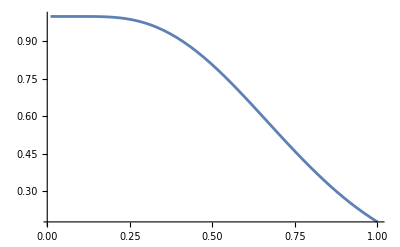

```mathematica
Plot[Exp[2 x(Log[1 - Exp[-1/x]]-x PolyLog[2,Exp[-1/x]])],{x,0.01,1}]
```

```mathematica
X1 =(b + I a) Sqrt[1 + 4 S^2/(b+ I a)^2]
X2 =(b - I a) Sqrt[1 + 4 S^2/(b- I a)^2]
X1approx=(b+I a) Sqrt[1 - (2b+ 4 S^2)/a^2]
X2approx = (b-I a) Sqrt[1 +(2b - 4 S^2)/a^2]
Residue[(1/(4 Pi)) (a b Exp[-M x]/x) Cosh[x b Sqrt[1 - 4 S^2/a^2]] Cos[x a Sqrt[1 - 4 S^2/a^2]]/(Sin[a x] Sinh[b x]),{x, Pi/a}]//ExpandAll//Evaluate//FullSimplify
```

(ⅈ a+b) √(1+(4 S^2)/(ⅈ a+b)^2)

(-ⅈ a+b) √(1+(4 S^2)/(-ⅈ a+b)^2)

(ⅈ a+b) √(1-(4 S^2)/a^2)

(-ⅈ a+b) √(1-(4 S^2)/a^2)

-(a b ⅇ^(-(M π)/a) Cos[π √(1-(4 S^2)/a^2)] Cosh[(b π √(1-(4 S^2)/a^2))/a] Csch[(b π)/a])/(2 π^2)

```mathematica
Residue[(1/(2 Pi)) (a b Exp[-M x]/x) Cosh[x b Sqrt[1 - 4 S^2/a^2]] Cos[x a Sqrt[1 - 4 S^2/a^2]]/(Sin[a x] Sinh[b x]),{x, 2 Pi/a}]//ExpandAll//Evaluate//FullSimplify
```

(a b ⅇ^(-(2 M π)/a) Cos[2 π √(1-(4 S^2)/a^2)] Cosh[(2 b π √(1-(4 S^2)/a^2))/a] Csch[(2 b π)/a])/(4 π^2)

```mathematica
Residue[(1/(2 Pi)) (a b Exp[-M x]/x) Cosh[x b Sqrt[1 - 4 S^2/a^2]] Cos[x a Sqrt[1 - 4 S^2/a^2]]/(Sin[a x] Sinh[b x]),{x, 3 Pi/a}]//ExpandAll//Evaluate//FullSimplify
```

-(a b ⅇ^(-(3 M π)/a) Cos[3 π √(1-(4 S^2)/a^2)] Cosh[(3 b π √(1-(4 S^2)/a^2))/a] Csch[(3 b π)/a])/(6 π^2)

```mathematica
Cos[a Sqrt[(b + c)^2 - d^2]] + Cos[a Sqrt[(b - c)^2 - d^2]]//FullSimplify
```

Cos[a √((b+c-d) (b+c+d))]+Cos[a √((b-c)^2-d^2)]

```mathematica
Mp = 1.22*^19
g = 106.75
```

1.22×10^19

106.75

```mathematica
2 ((2 Pi)^3)/Sqrt[45 Mp] Power[4 g^3/((Zeta[3])^2),1/4]1.697369//Evaluate
```

1.53953×10^-6

```mathematica
res = 1.53953 10^(-11)
nS = res Sqrt[(10^(-3))/(10^(-1/2))]//Evaluate
```

1.53953×10^-11

8.65741×10^-13

```mathematica
nSt =Sqrt[(3.91/g) ((2.73 10^(-13)))^3] nS
```

2.3634×10^-32

```mathematica
NST = nSt/(Mp^(3/2))
```

5.54622×10^-61

```mathematica
(3/2) NST^2 Mp^2
```

6.86759×10^-83

```mathematica
LL=-Exp[-x (m^2 - S^2)] ((El^2 Cos[2 x El Sqrt[1-m^2 S^2/El^2]])/(x (Sin[x El])^2)- 2/(x^3)+4(El^2-m^2 S^2)/(3 x))
LR=-Exp[-x (m^2 - S^2)] ((El^2 Cosh[2 x m S])/(x (Sin[x El])^2)- 2/(x^3)+4(El^2-m^2 S^2)/(3 x))
LRalt = -Exp[-x (m^2 - S^2)]( (El^2 Cos[2 x m S])/(x (Sin[x El])^2)- 2/(x^3)+4(El^2+m^2 S^2)/(3 x))
Lfull = LL + LR//ExpandAll//Evaluate//FullSimplify
Lfullalt = LL + LRalt//ExpandAll//Evaluate//FullSimplify
```

-ⅇ^(-((m^2-S^2) x)) (-2/x^3+(4 (El^2-m^2 S^2))/(3 x)+(El^2 Cos[2 El √(1-(m^2 S^2)/El^2) x] Csc[El x]^2)/x)

-ⅇ^(-((m^2-S^2) x)) (-2/x^3+(4 (El^2-m^2 S^2))/(3 x)+(El^2 Cosh[2 m S x] Csc[El x]^2)/x)

-ⅇ^(-((m^2-S^2) x)) (-2/x^3+(4 (El^2+m^2 S^2))/(3 x)+(El^2 Cos[2 m S x] Csc[El x]^2)/x)

(ⅇ^((-m^2+S^2) x) (12-8 (El-m S) (El+m S) x^2-3 El^2 x^2 (Cos[2 El √(1-(m^2 S^2)/El^2) x]+Cosh[2 m S x]) Csc[El x]^2))/(3 x^3)

(ⅇ^((-m^2+S^2) x) (12-8 El^2 x^2-3 El^2 x^2 (Cos[2 m S x]+Cos[2 El √(1-(m^2 S^2)/El^2) x]) Csc[El x]^2))/(3 x^3)

```mathematica
Residue[LL,{x, Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LR,{x, Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LRalt,{x, Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[Lfull,{x, Pi/El}]//Evaluate//Simplify
Residue[Lfullalt,{x, Pi/El}]//Evaluate//Simplify
```

(ⅇ^((π (-m^2+S^2))/El) El ((El+π (m^2-S^2)) Cos[2 π √(1-(m^2 S^2)/El^2)]+2 El π √(1-(m^2 S^2)/El^2) Sin[2 π √(1-(m^2 S^2)/El^2)]))/π^2

(ⅇ^((π (-m^2+S^2))/El) El ((El+π (m^2-S^2)) Cosh[(2 m π S)/El]-2 m π S Sinh[(2 m π S)/El]))/π^2

(ⅇ^((π (-m^2+S^2))/El) El ((El+π (m^2-S^2)) Cos[(2 m π S)/El]+2 m π S Sin[(2 m π S)/El]))/π^2

1/π^2 ⅇ^((π (-m^2+S^2))/El) El (El Cos[2 π √(1-(m^2 S^2)/El^2)]+m^2 π Cos[2 π √(1-(m^2 S^2)/El^2)]-π S^2 Cos[2 π √(1-(m^2 S^2)/El^2)]+(El+π (m^2-S^2)) Cosh[(2 m π S)/El]+2 El π √(1-(m^2 S^2)/El^2) Sin[2 π √(1-(m^2 S^2)/El^2)]-2 m π S Sinh[(2 m π S)/El])

(ⅇ^((π (-m^2+S^2))/El) El ((El+π (m^2-S^2)) Cos[(2 m π S)/El]+(El+m^2 π-π S^2) Cos[2 π √(1-(m^2 S^2)/El^2)]+2 m π S Sin[(2 m π S)/El]+2 El π √(1-(m^2 S^2)/El^2) Sin[2 π √(1-(m^2 S^2)/El^2)]))/π^2

```mathematica
Residue[LL,{x, 2 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LR,{x, 2 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LRalt,{x, 2 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[Lfull,{x, 2 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[Lfullalt,{x, 2  Pi/El}]//ExpandAll//Evaluate//Simplify
```

(ⅇ^(-(2 π (m^2-S^2))/El) El ((El+2 π (m^2-S^2)) Cos[4 π √(1-(m^2 S^2)/El^2)]+4 El π √(1-(m^2 S^2)/El^2) Sin[4 π √(1-(m^2 S^2)/El^2)]))/(4 π^2)

(ⅇ^(-(2 π (m^2-S^2))/El) El ((El+2 π (m^2-S^2)) Cosh[(4 m π S)/El]-4 m π S Sinh[(4 m π S)/El]))/(4 π^2)

(ⅇ^(-(2 π (m^2-S^2))/El) El ((El+2 π (m^2-S^2)) Cos[(4 m π S)/El]+4 m π S Sin[(4 m π S)/El]))/(4 π^2)

1/(4 π^2)ⅇ^(-(2 π (m^2-S^2))/El) El (El Cos[4 π √(1-(m^2 S^2)/El^2)]+2 m^2 π Cos[4 π √(1-(m^2 S^2)/El^2)]-2 π S^2 Cos[4 π √(1-(m^2 S^2)/El^2)]+(El+2 π (m^2-S^2)) Cosh[(4 m π S)/El]+4 El π √(1-(m^2 S^2)/El^2) Sin[4 π √(1-(m^2 S^2)/El^2)]-4 m π S Sinh[(4 m π S)/El])

1/(4 π^2)ⅇ^(-(2 π (m^2-S^2))/El) El ((El+2 π (m^2-S^2)) Cos[(4 m π S)/El]+(El+2 m^2 π-2 π S^2) Cos[4 π √(1-(m^2 S^2)/El^2)]+4 m π S Sin[(4 m π S)/El]+4 El π √(1-(m^2 S^2)/El^2) Sin[4 π √(1-(m^2 S^2)/El^2)])

```mathematica
Residue[LL,{x,3 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LR,{x,3 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[LRalt,{x,3 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[Lfull,{x,3 Pi/El}]//ExpandAll//Evaluate//Simplify
Residue[Lfullalt,{x,3Pi/El}]//ExpandAll//Evaluate//Simplify
```

(ⅇ^(-(3 π (m^2-S^2))/El) El ((El+3 π (m^2-S^2)) Cos[6 π √(1-(m^2 S^2)/El^2)]+6 El π √(1-(m^2 S^2)/El^2) Sin[6 π √(1-(m^2 S^2)/El^2)]))/(9 π^2)

(ⅇ^(-(3 π (m^2-S^2))/El) El ((El+3 π (m^2-S^2)) Cosh[(6 m π S)/El]-6 m π S Sinh[(6 m π S)/El]))/(9 π^2)

(ⅇ^(-(3 π (m^2-S^2))/El) El ((El+3 π (m^2-S^2)) Cos[(6 m π S)/El]+6 m π S Sin[(6 m π S)/El]))/(9 π^2)

1/(9 π^2)ⅇ^(-(3 π (m^2-S^2))/El) El (El Cos[6 π √(1-(m^2 S^2)/El^2)]+3 m^2 π Cos[6 π √(1-(m^2 S^2)/El^2)]-3 π S^2 Cos[6 π √(1-(m^2 S^2)/El^2)]+(El+3 π (m^2-S^2)) Cosh[(6 m π S)/El]+6 El π √(1-(m^2 S^2)/El^2) Sin[6 π √(1-(m^2 S^2)/El^2)]-6 m π S Sinh[(6 m π S)/El])

1/(9 π^2)ⅇ^(-(3 π (m^2-S^2))/El) El ((El+3 π (m^2-S^2)) Cos[(6 m π S)/El]+(El+3 m^2 π-3 π S^2) Cos[6 π √(1-(m^2 S^2)/El^2)]+6 m π S Sin[(6 m π S)/El]+6 El π √(1-(m^2 S^2)/El^2) Sin[6 π √(1-(m^2 S^2)/El^2)])

```mathematica
ratefull = Collect[∑_(n=1)^∞ 1/(n^2 π^2)ⅇ^(-(n π (m^2-S^2))/El) El (El Cos[2 n π √(1-(m^2 S^2)/El^2)]+n m^2 π Cos[2 n π √(1-(m^2 S^2)/El^2)]-n π S^2 Cos[2 n π √(1-(m^2 S^2)/El^2)]+(El+n π (m^2-S^2)) Cosh[(2 n m π S)/El]+2 n El π √(1-(m^2 S^2)/El^2) Sin[2 n π √(1-(m^2 S^2)/El^2)]-2 n m π S Sinh[(2 n m π S)/El])//ExpandAll//Evaluate//FullSimplify,{m,S,El}]
```

(El m S (-2 π Log[1-ⅇ^((π (-m^2-2 m S+S^2))/El)]+2 π Log[1-ⅇ^((π (-m^2+2 m S+S^2))/El)]))/(2 π^2)+(El m^2 (-π Log[1-ⅇ^((π (-m^2-2 m S+S^2))/El)]-π Log[1-ⅇ^((π (-m^2+2 m S+S^2))/El)]-π Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]-π Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]))/(2 π^2)+(El S^2 (π Log[1-ⅇ^((π (-m^2-2 m S+S^2))/El)]+π Log[1-ⅇ^((π (-m^2+2 m S+S^2))/El)]+π Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+π Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]))/(2 π^2)+1/(2 π^2)El^2 (-2 ⅈ π √(1-(m^2 S^2)/El^2) Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+2 ⅈ π √(1-(m^2 S^2)/El^2) Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+PolyLog[2,ⅇ^((π (-m^2-2 m S+S^2))/El)]+PolyLog[2,ⅇ^((π (-m^2+2 m S+S^2))/El)]+PolyLog[2,ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+PolyLog[2,ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)])

```mathematica
ratefullalt = Collect[∑_(n=1)^∞ 1/(n^2  π^2)ⅇ^(-(n π (m^2-S^2))/El) El ((El+n π (m^2-S^2)) Cos[(2 n m π S)/El]+(El+n m^2 π-n π S^2) Cos[2 n π √(1-(m^2 S^2)/El^2)]+2 n m π S Sin[(2 n m π S)/El]+2 n El π √(1-(m^2 S^2)/El^2) Sin[2 n π √(1-(m^2 S^2)/El^2)])//ExpandAll//Evaluate//FullSimplify,{m,S,El}]
```

(El m S (2 ⅈ π Log[1-ⅇ^(-(π (m-ⅈ S)^2)/El)]-2 ⅈ π Log[1-ⅇ^(-(π (m+ⅈ S)^2)/El)]))/(2 π^2)+(El m^2 (-π Log[1-ⅇ^(-(π (m-ⅈ S)^2)/El)]-π Log[1-ⅇ^(-(π (m+ⅈ S)^2)/El)]-π Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]-π Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]))/(2 π^2)+(El S^2 (π Log[1-ⅇ^(-(π (m-ⅈ S)^2)/El)]+π Log[1-ⅇ^(-(π (m+ⅈ S)^2)/El)]+π Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+π Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]))/(2 π^2)+1/(2 π^2)El^2 (-2 ⅈ π √(1-(m^2 S^2)/El^2) Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+2 ⅈ π √(1-(m^2 S^2)/El^2) Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+PolyLog[2,ⅇ^(-(π (m-ⅈ S)^2)/El)]+PolyLog[2,ⅇ^(-(π (m+ⅈ S)^2)/El)]+PolyLog[2,ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+PolyLog[2,ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)])

```mathematica
rateL = ∑_(n=1)^∞ (ⅇ^(-(n π (m^2-S^2))/El) El ((El+n π (m^2-S^2)) Cos[2 n π √(1-(m^2 S^2)/El^2)]+2 n El π √(1-(m^2 S^2)/El^2) Sin[2 n π √(1-(m^2 S^2)/El^2)]))/(n^2 π^2)//ExpandAll//Evaluate//FullSimplify
rateLs = ∑_(n=1)^∞ (ⅇ^(-(n π (1-s^2))/e) e ((e+n π (1-s^2)) Cos[2 n π √(1-s^2/e^2)]+2 n e π √(1-s^2/e^2) Sin[2 n π √(1-s^2/e^2)]))/(n^2 π^2)//ExpandAll//Evaluate//FullSimplify
```

1/(2 π^2)El (π (-m^2+S^2-2 ⅈ El √(1-(m^2 S^2)/El^2)) Log[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+π (-m^2+S^2+2 ⅈ El √(1-(m^2 S^2)/El^2)) Log[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+El PolyLog[2,ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)]+El PolyLog[2,ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)])

1/(2 π^2)e (π (-1+s^2-2 ⅈ e √(1-s^2/e^2)) Log[1-ⅇ^((π (-1+s^2-2 ⅈ e √(1-s^2/e^2)))/e)]+π (-1+s^2+2 ⅈ e √(1-s^2/e^2)) Log[1-ⅇ^((π (-1+s^2+2 ⅈ e √(1-s^2/e^2)))/e)]+e PolyLog[2,ⅇ^((π (-1+s^2-2 ⅈ e √(1-s^2/e^2)))/e)]+e PolyLog[2,ⅇ^((π (-1+s^2+2 ⅈ e √(1-s^2/e^2)))/e)])

```mathematica
rateR = ∑_(n=1)^∞ (ⅇ^(-(n π (m^2-S^2))/El) El ((El+n π (m^2-S^2)) Cosh[(2 n m π S)/El]-2 n m π S Sinh[(2 n m π S)/El]))/(n^2 π^2)//ExpandAll//Evaluate//FullSimplify
rateRs = ∑_(n=1)^∞ (ⅇ^(-(n π (1-s^2))/e) e ((e+n π (1-s^2)) Cosh[(2 n m π s)/e]-2 n π s Sinh[(2 n π s)/e]))/(n^2 π^2)//ExpandAll//Evaluate//FullSimplify
```

1/(2 π^2)El (π (-m^2-2 m S+S^2) Log[1-ⅇ^((π (-m^2-2 m S+S^2))/El)]+π (-m^2+2 m S+S^2) Log[1-ⅇ^((π (-m^2+2 m S+S^2))/El)]+El (PolyLog[2,ⅇ^((π (-m^2-2 m S+S^2))/El)]+PolyLog[2,ⅇ^((π (-m^2+2 m S+S^2))/El)]))

1/(2 π^2)e (π (-2 s Log[1-ⅇ^((π (-1+(-2+s) s))/e)]+(-1+s^2) (Log[1-ⅇ^((π (-1-2 m s+s^2))/e)]+Log[1-ⅇ^((π (-1+2 m s+s^2))/e)])+2 s Log[1-ⅇ^((π (-1+s (2+s)))/e)])+e (PolyLog[2,ⅇ^((π (-1-2 m s+s^2))/e)]+PolyLog[2,ⅇ^((π (-1+2 m s+s^2))/e)]))

```mathematica
rateRalt = ∑_(n=1)^∞ (ⅇ^(-(n π (m^2-S^2))/El) El ((El+n π (m^2-S^2)) Cos[(2 n m π S)/El]+2 n m π S Sin[(2 n m π S)/El]))/(n^2 π^2)//ExpandAll//Evaluate//FullSimplify
```

(El (-π (m-ⅈ S)^2 Log[1-ⅇ^(-(π (m-ⅈ S)^2)/El)]-π (m+ⅈ S)^2 Log[1-ⅇ^(-(π (m+ⅈ S)^2)/El)]+El (PolyLog[2,ⅇ^(-(π (m-ⅈ S)^2)/El)]+PolyLog[2,ⅇ^(-(π (m+ⅈ S)^2)/El)])))/(2 π^2)

```mathematica
rateL/.S->m//ExpandAll//Evaluate//FullSimplify
rateR/.S->m//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->m//ExpandAll//Evaluate//FullSimplify
ratefull/.S->m//ExpandAll//Evaluate//FullSimplify
ratefullalt/.S->m//ExpandAll//Evaluate//FullSimplify
```

(El^2 (-2 ⅈ √(1-m^4/El^2) π (Log[1-ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]-Log[1-ⅇ^(2 ⅈ √(1-m^4/El^2) π)])+PolyLog[2,ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]+PolyLog[2,ⅇ^(2 ⅈ √(1-m^4/El^2) π)]))/(2 π^2)

(El (2 m^2 π (-Log[1-ⅇ^(-(2 m^2 π)/El)]+Log[1-ⅇ^((2 m^2 π)/El)])+El (PolyLog[2,ⅇ^(-(2 m^2 π)/El)]+PolyLog[2,ⅇ^((2 m^2 π)/El)])))/(2 π^2)

(El (-2 ⅈ m^2 π (Log[1-ⅇ^(-(2 ⅈ m^2 π)/El)]-Log[1-ⅇ^((2 ⅈ m^2 π)/El)])+El (PolyLog[2,ⅇ^(-(2 ⅈ m^2 π)/El)]+PolyLog[2,ⅇ^((2 ⅈ m^2 π)/El)])))/(2 π^2)

1/(2 π^2)El (-2 m^2 π Log[1-ⅇ^(-(2 m^2 π)/El)]+2 m^2 π Log[1-ⅇ^((2 m^2 π)/El)]-2 ⅈ El √(1-m^4/El^2) π (Log[1-ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]-Log[1-ⅇ^(2 ⅈ √(1-m^4/El^2) π)])+El (PolyLog[2,ⅇ^(-(2 m^2 π)/El)]+PolyLog[2,ⅇ^((2 m^2 π)/El)]+PolyLog[2,ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]+PolyLog[2,ⅇ^(2 ⅈ √(1-m^4/El^2) π)]))

1/(2 π^2)El (-2 ⅈ π (m^2 (Log[1-ⅇ^(-(2 ⅈ m^2 π)/El)]-Log[1-ⅇ^((2 ⅈ m^2 π)/El)])+El √(1-m^4/El^2) (Log[1-ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]-Log[1-ⅇ^(2 ⅈ √(1-m^4/El^2) π)]))+El (PolyLog[2,ⅇ^(-(2 ⅈ m^2 π)/El)]+PolyLog[2,ⅇ^((2 ⅈ m^2 π)/El)]+PolyLog[2,ⅇ^(-2 ⅈ √(1-m^4/El^2) π)]+PolyLog[2,ⅇ^(2 ⅈ √(1-m^4/El^2) π)]))

```mathematica
rateL/.S->m/.El->4 m^2/Sqrt[15]//ExpandAll//Evaluate//FullSimplify
rateR/.S->m/.El->4 m^2/Sqrt[15]//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->m/.El->4 m^2/Sqrt[15]//ExpandAll//Evaluate//FullSimplify
ratefull/.S->m/.El->4 m^2/Sqrt[15]//ExpandAll//Evaluate//FullSimplify
ratefullalt/.S->m/.El->4 m^2/Sqrt[15]//ExpandAll//Evaluate//FullSimplify
```

m^4/9

(53 m^4)/45

-(37 m^4)/45

(58 m^4)/45

-(32 m^4)/45

```mathematica
rateL/.S->m/.El->4 m^2/Sqrt[7]//ExpandAll//Evaluate//FullSimplify
rateR/.S->m/.El->4 m^2/Sqrt[7]//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->m/.El->4 m^2/Sqrt[7]//ExpandAll//Evaluate//FullSimplify
ratefull/.S->m/.El->4 m^2/Sqrt[7]//ExpandAll//Evaluate//FullSimplify
ratefullalt/.S->m/.El->4 m^2/Sqrt[7]//ExpandAll//Evaluate//FullSimplify
```

-(19 m^4)/21

(29 m^4)/21

-(13 m^4)/21

(10 m^4)/21

-(32 m^4)/21

```mathematica
NSolve[{(rateLs/.s->1.0//ExpandAll//Evaluate//FullSimplify)==0,e>(Sqrt[16.0/15.0]//Evaluate),e<(Sqrt[16.0/7.0]//Evaluate)},e]//ExpandAll//Evaluate//FullSimplify
```

{{e→1.09545}}

```mathematica
rateLs/.s->1.0/.e->1.0954451150103321//ExpandAll//Evaluate//FullSimplify
```

1.47871×10^-16+0. ⅈ

```mathematica
NSolve[{(rateLs/.e->1.0//ExpandAll//Evaluate//FullSimplify)==0,s>(Sqrt[7.0/15.0]//Evaluate),s<(Sqrt[15.0/7.0]//Evaluate)},s]//ExpandAll//Evaluate//FullSimplify
```

{{s→0.92179}}

```mathematica
NSolve[{(rateLs/.s->Sqrt[1.0-(9.785 10^(-10))^2]//ExpandAll//Evaluate//FullSimplify)==0,e>(Sqrt[16.0/15.0]//Evaluate),e<(Sqrt[16.0/7.0]//Evaluate)},e]//ExpandAll//Evaluate//FullSimplify
```

{{e→1.09545}}

```mathematica
Reduce[{(rateLs//ExpandAll//Evaluate)==0,s>(Sqrt[7.0/15.0]//Evaluate),s<(Sqrt[15.0/7.0]//Evaluate)},s]//ExpandAll//Evaluate//FullSimplify
```

$Aborted

```mathematica
Limit[rateL/.El->m^2,S->m]//ExpandAll//Evaluate//FullSimplify
Limit[rateR/.El->m^2,S->m]//ExpandAll//Evaluate//FullSimplify
Limit[rateRalt/.El->m^2,S->m]//ExpandAll//Evaluate//FullSimplify
```

m^4/6

(7 m^4)/6

Indeterminate

```mathematica
Limit[ratefull/.El->m^2,S->m]//ExpandAll//Evaluate//FullSimplify
Limit[ratefullalt/.El->m^2,S->m]//ExpandAll//Evaluate//FullSimplify
```

(4 m^4)/3

Indeterminate

```mathematica
Limit[rateL/.S->m/2,El->m^2]//ExpandAll//Evaluate//FullSimplify
rateR/.S->m/2/.El->m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->m/2/.El->m^2//ExpandAll//Evaluate//FullSimplify
```

1/(8 π^2)m^4 ((9 π^2)/4-8 √3 π ArcCot[Cot[√3 π]-ⅇ^(3 π/4) Csc[√3 π]]-3 π Log[-2 Cos[√3 π]+2 Cosh[(3 π)/4]]+4 (PolyLog[2,ⅇ^((-3/4-ⅈ √3) π)]+PolyLog[2,ⅇ^((-3/4+ⅈ √3) π)]))

(m^4 (π (ⅈ π-7 Log[1-ⅇ^(-7 π/4)]+Log[-1+ⅇ^(π/4)])+4 (PolyLog[2,ⅇ^(-7 π/4)]+PolyLog[2,ⅇ^(π/4)])))/(8 π^2)

(m^4 (-3 π Log[1+ⅇ^(-3 π/4)]+4 PolyLog[2,-ⅇ^(-3 π/4)]))/(4 π^2)

```mathematica
rateL/.El->m^2//ExpandAll//Evaluate//FullSimplify
rateR/.El->m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.El->m^2//ExpandAll//Evaluate//FullSimplify
```

1/(2 π^2)m^2 (π (S^2+m^2 (-1-2 ⅈ √(1-S^2/m^2))) Log[1-ⅇ^(π (-1+S^2/m^2-2 ⅈ √(1-S^2/m^2)))]+π (S^2+m^2 (-1+2 ⅈ √(1-S^2/m^2))) Log[1-ⅇ^(π (-1+S^2/m^2+2 ⅈ √(1-S^2/m^2)))]+m^2 (PolyLog[2,ⅇ^(π (-1+S^2/m^2-2 ⅈ √(1-S^2/m^2)))]+PolyLog[2,ⅇ^(π (-1+S^2/m^2+2 ⅈ √(1-S^2/m^2)))]))

1/(2 π^2)m^2 (π (-m^2-2 m S+S^2) Log[1-ⅇ^((π (-m^2-2 m S+S^2))/m^2)]+π (-m^2+2 m S+S^2) Log[1-ⅇ^(π (-1+(S (2 m+S))/m^2))]+m^2 (PolyLog[2,ⅇ^((π (-m^2-2 m S+S^2))/m^2)]+PolyLog[2,ⅇ^((π (-m^2+2 m S+S^2))/m^2)]))

(m^2 (-π (m-ⅈ S)^2 Log[1-ⅇ^(-(π (m-ⅈ S)^2)/m^2)]-π (m+ⅈ S)^2 Log[1-ⅇ^(-(π (m+ⅈ S)^2)/m^2)]+m^2 (PolyLog[2,ⅇ^(-(π (m-ⅈ S)^2)/m^2)]+PolyLog[2,ⅇ^(-(π (m+ⅈ S)^2)/m^2)])))/(2 π^2)

```mathematica
rateL/.El->-m^2//ExpandAll//Evaluate//FullSimplify
rateR/.El->-m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.El->-m^2//ExpandAll//Evaluate//FullSimplify
```

1/(2 π^2)m^2 (π (-S^2+m^2 (1-2 ⅈ √(1-S^2/m^2))) Log[1-ⅇ^(π (1-S^2/m^2-2 ⅈ √(1-S^2/m^2)))]+π (-S^2+m^2 (1+2 ⅈ √(1-S^2/m^2))) Log[1-ⅇ^(π (1-S^2/m^2+2 ⅈ √(1-S^2/m^2)))]+m^2 (PolyLog[2,ⅇ^(π (1-S^2/m^2-2 ⅈ √(1-S^2/m^2)))]+PolyLog[2,ⅇ^(π (1-S^2/m^2+2 ⅈ √(1-S^2/m^2)))]))

1/(2 π^2)m^2 (π (m^2-2 m S-S^2) Log[1-ⅇ^((π (m^2-2 m S-S^2))/m^2)]+π (m^2+2 m S-S^2) Log[1-ⅇ^((π (m^2+2 m S-S^2))/m^2)]+m^2 (PolyLog[2,ⅇ^((π (m^2-2 m S-S^2))/m^2)]+PolyLog[2,ⅇ^((π (m^2+2 m S-S^2))/m^2)]))

(m^2 (π (m-ⅈ S)^2 Log[1-ⅇ^((π (m-ⅈ S)^2)/m^2)]+π (m+ⅈ S)^2 Log[1-ⅇ^((π (m+ⅈ S)^2)/m^2)]+m^2 (PolyLog[2,ⅇ^((π (m-ⅈ S)^2)/m^2)]+PolyLog[2,ⅇ^((π (m+ⅈ S)^2)/m^2)])))/(2 π^2)

```mathematica
rateL/.El->m^2/.S->0//ExpandAll//Evaluate//FullSimplify
rateR/.El->m^2/.S->0//ExpandAll//Evaluate//FullSimplify
rateRalt/.El->m^2/.S->0//ExpandAll//Evaluate//FullSimplify
```

(m^4 (π^2-π Log[-1+ⅇ^π]+PolyLog[2,ⅇ^-π]))/π^2

(m^4 (π^2-π Log[-1+ⅇ^π]+PolyLog[2,ⅇ^-π]))/π^2

(m^4 (π^2-π Log[-1+ⅇ^π]+PolyLog[2,ⅇ^-π]))/π^2

```mathematica
rateL/.El->-m^2/.S->0//ExpandAll//Evaluate//FullSimplify
rateR/.El->-m^2/.S->0//ExpandAll//Evaluate//FullSimplify
rateRalt/.El->-m^2/.S->0//ExpandAll//Evaluate//FullSimplify
```

(m^4 (π (ⅈ π+Log[-1+ⅇ^π])+PolyLog[2,ⅇ^π]))/π^2

(m^4 (π (ⅈ π+Log[-1+ⅇ^π])+PolyLog[2,ⅇ^π]))/π^2

(m^4 (π (ⅈ π+Log[-1+ⅇ^π])+PolyLog[2,ⅇ^π]))/π^2

```mathematica
rateL/.S->2m/.El->m^2/2//ExpandAll//Evaluate//FullSimplify
rateR/.S->2m/.El->m^2/2//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->2m/.El->m^2/4//ExpandAll//Evaluate//FullSimplify
```

1/(8 π^2)m^4 (2 ⅈ (3+√15) π^2-2 (-3+√15) π Log[1-ⅇ^(-2 (-3+√15) π)]+2 (3+√15) π Log[-1+ⅇ^(2 (3+√15) π)]+PolyLog[2,ⅇ^(-2 (-3+√15) π)]+PolyLog[2,ⅇ^(2 (3+√15) π)])

(m^4 (2 π ((2+7 ⅈ) π-Log[-1+ⅇ^(2 π)]+7 Log[-1+ⅇ^(14 π)])+PolyLog[2,ⅇ^(-2 π)]+PolyLog[2,ⅇ^(14 π)]))/(8 π^2)

(m^4 (12 π (ⅈ π+Log[-1+ⅇ^(12 π)])+PolyLog[2,ⅇ^(12 π)]))/(16 π^2)

```mathematica
PolyLog[2,1]
```

π^2/6

```mathematica
Reduce[15 - 4 k^2 - 4 k>0&&k>=0,k, Integers]
Reduce[3 - 4 k^2 - 4 k>0&&k>=0,k, Integers]
```

k==0||k==1

k==0

```mathematica
rateL/.S->(Sqrt[15/16] El/m)//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[15/16] El/m)//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[15/16] El/m)//ExpandAll//Evaluate//FullSimplify
```

(El (16 El m^2 π ArcCot[ⅇ^(-(15 El π)/(16 m^2)+(m^2 π)/El)]+(15 El^2-16 m^4) π (Log[1-ⅈ ⅇ^((15 El π)/(16 m^2)-(m^2 π)/El)]+Log[1+ⅈ ⅇ^((15 El π)/(16 m^2)-(m^2 π)/El)])+8 El m^2 PolyLog[2,-ⅇ^((15 El π)/(8 m^2)-(2 m^2 π)/El)]))/(32 m^2 π^2)

1/(32 m^2 π^2)El ((15 El^2-8 √15 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (-8 √15+(15 El)/m^2-(16 m^2)/El) π)]+(15 El^2+8 √15 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (8 √15+(15 El)/m^2-(16 m^2)/El) π)]+16 El m^2 (PolyLog[2,ⅇ^(1/16 (-8 √15+(15 El)/m^2-(16 m^2)/El) π)]+PolyLog[2,ⅇ^(1/16 (8 √15+(15 El)/m^2-(16 m^2)/El) π)]))

1/(32 m^2 π^2)El ((15 El^2-8 ⅈ √15 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (-8 ⅈ √15+(15 El)/m^2-(16 m^2)/El) π)]+(15 El^2+8 ⅈ √15 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (8 ⅈ √15+(15 El)/m^2-(16 m^2)/El) π)]+16 El m^2 (PolyLog[2,ⅇ^(1/16 (-8 ⅈ √15+(15 El)/m^2-(16 m^2)/El) π)]+PolyLog[2,ⅇ^(1/16 (8 ⅈ √15+(15 El)/m^2-(16 m^2)/El) π)]))

```mathematica
rateL/.S->(Sqrt[15/16] El/m)/.El->Sqrt[16/15] m^2//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[15/16] El/m)/.El->Sqrt[16/15] m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[15/16] El/m)/.El->Sqrt[16/15] m^2//ExpandAll//Evaluate//FullSimplify
```

m^4/9

(53 m^4)/45

-(37 m^4)/45

```mathematica
rateL/.S->(Sqrt[7/16] El/m)//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[7/16] El/m)//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[7/16] El/m)//ExpandAll//Evaluate//FullSimplify
```

(El (-48 El m^2 π ArcCot[ⅇ^(-(7 El π)/(16 m^2)+(m^2 π)/El)]+(7 El^2-16 m^4) π (Log[1-ⅈ ⅇ^((7 El π)/(16 m^2)-(m^2 π)/El)]+Log[1+ⅈ ⅇ^((7 El π)/(16 m^2)-(m^2 π)/El)])+8 El m^2 PolyLog[2,-ⅇ^((7 El π)/(8 m^2)-(2 m^2 π)/El)]))/(32 m^2 π^2)

1/(32 m^2 π^2)El ((7 El^2-8 √7 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (-8 √7+(7 El)/m^2-(16 m^2)/El) π)]+(7 El^2+8 √7 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (8 √7+(7 El)/m^2-(16 m^2)/El) π)]+16 El m^2 (PolyLog[2,ⅇ^(1/16 (-8 √7+(7 El)/m^2-(16 m^2)/El) π)]+PolyLog[2,ⅇ^(1/16 (8 √7+(7 El)/m^2-(16 m^2)/El) π)]))

1/(32 m^2 π^2)El ((7 El^2-8 ⅈ √7 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (-8 ⅈ √7+(7 El)/m^2-(16 m^2)/El) π)]+(7 El^2+8 ⅈ √7 El m^2-16 m^4) π Log[1-ⅇ^(1/16 (8 ⅈ √7+(7 El)/m^2-(16 m^2)/El) π)]+16 El m^2 (PolyLog[2,ⅇ^(1/16 (-8 ⅈ √7+(7 El)/m^2-(16 m^2)/El) π)]+PolyLog[2,ⅇ^(1/16 (8 ⅈ √7+(7 El)/m^2-(16 m^2)/El) π)]))

```mathematica
rateL/.S->(Sqrt[7/16] El/m)/.El->Sqrt[16/7] m^2//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[7/16] El/m)/.El->Sqrt[16/7] m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[7/16] El/m)/.El->Sqrt[16/7] m^2//ExpandAll//Evaluate//FullSimplify
```

-(19 m^4)/21

(29 m^4)/21

-(13 m^4)/21

```mathematica
Reduce[rateL==0&&(Sqrt[7/15] m)<S<(Sqrt[15/7]m)&&Sqrt[16/15] m^2<El<Sqrt[16/7] m^2,{S,El}]//ExpandAll//Evaluate//FullSimplify
```

```mathematica
rateL/.S->(Sqrt[3/4] El/m)//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[3/4] El/m)//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[3/4] El/m)//ExpandAll//Evaluate//FullSimplify
```

(El ((3 El^2-4 m^4) π Log[1+ⅇ^((3 El π)/(4 m^2)-(m^2 π)/El)]+4 El m^2 PolyLog[2,-ⅇ^((3 El π)/(4 m^2)-(m^2 π)/El)]))/(4 m^2 π^2)

1/(8 m^2 π^2)El ((3 El^2-4 √3 El m^2-4 m^4) π Log[1-ⅇ^((-√3+(3 El)/(4 m^2)-m^2/El) π)]+(3 El^2+4 √3 El m^2-4 m^4) π Log[1-ⅇ^((√3+(3 El)/(4 m^2)-m^2/El) π)]+4 El m^2 (PolyLog[2,ⅇ^((-√3+(3 El)/(4 m^2)-m^2/El) π)]+PolyLog[2,ⅇ^((√3+(3 El)/(4 m^2)-m^2/El) π)]))

1/(8 m^2 π^2)El ((3 El^2-4 ⅈ √3 El m^2-4 m^4) π Log[1-ⅇ^((-ⅈ √3+(3 El)/(4 m^2)-m^2/El) π)]+(3 El^2+4 ⅈ √3 El m^2-4 m^4) π Log[1-ⅇ^((ⅈ √3+(3 El)/(4 m^2)-m^2/El) π)]+4 El m^2 (PolyLog[2,ⅇ^((-ⅈ √3+(3 El)/(4 m^2)-m^2/El) π)]+PolyLog[2,ⅇ^((ⅈ √3+(3 El)/(4 m^2)-m^2/El) π)]))

```mathematica
rateL/.S->(Sqrt[3/4] El/m)/.El->Sqrt[4/3] m^2//ExpandAll//Evaluate//FullSimplify
rateR/.S->(Sqrt[3/4] El/m)/.El->Sqrt[4/3] m^2//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->(Sqrt[3/4] El/m)/.El->Sqrt[4/3] m^2//ExpandAll//Evaluate//FullSimplify
```

-m^4/9

(11 m^4)/9

-(7 m^4)/9

```mathematica
Reduce[rateR==0,{S,El}]//ExpandAll//Evaluate//FullSimplify
```

1/(4 π^2)El (4 El π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Arg[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)] Cos[1/2 Arg[1-(m^2 S^2)/El^2]]-4 El π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Arg[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)] Cos[1/2 Arg[1-(m^2 S^2)/El^2]]-π (m-S) (m+S) (Log[1+ⅇ^(-(2 π (m^2-S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2-2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]]+Log[1+ⅇ^((2 π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]])+2 El (Re[PolyLog[2,ⅇ^((-m^2 π+π (S^2-2 ⅈ El √(1-(m^2 S^2)/El^2)))/El)]]+Re[PolyLog[2,ⅇ^((-m^2 π+π (S^2+2 ⅈ El √(1-(m^2 S^2)/El^2)))/El)]]+π (((El^2-m^2 S^2)^2)/El^4)^(1/4) (-Log[1+ⅇ^(-(2 π (m^2-S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2-2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]]+Log[1+ⅇ^((2 π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]]) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))

```mathematica
Reduce[rateL==0,{S,El}]//ExpandAll//Evaluate//FullSimplify
```

```mathematica
ComplexExpand[Im[rateL]]//ExpandAll//Evaluate//FullSimplify
```

1/(2 π^2)El (El (Im[PolyLog[2,ⅇ^((-m^2 π+π (S^2-2 ⅈ El √(1-(m^2 S^2)/El^2)))/El)]]+Im[PolyLog[2,ⅇ^((-m^2 π+π (S^2+2 ⅈ El √(1-(m^2 S^2)/El^2)))/El)]]+π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]] (Log[1+ⅇ^(-(2 π (m^2-S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2-2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]]-Log[1+ⅇ^((2 π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El)-2 ⅇ^((π (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))/El) Cos[2 π (((El^2-m^2 S^2)^2)/El^4)^(1/4) Cos[1/2 Arg[1-(m^2 S^2)/El^2]]]]))+π Arg[1-ⅇ^((-m^2 π+π S^2+2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)] (-m^2+S^2-2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]])+π Arg[1-ⅇ^((-m^2 π+π S^2-2 ⅈ El π √(1-(m^2 S^2)/El^2))/El)] (-m^2+S^2+2 El (((El^2-m^2 S^2)^2)/El^4)^(1/4) Sin[1/2 Arg[1-(m^2 S^2)/El^2]]))

```mathematica
rateL/.S->0//ExpandAll//Evaluate//FullSimplify
rateR/.S->0//ExpandAll//Evaluate//FullSimplify
rateRalt/.S->0//ExpandAll//Evaluate//FullSimplify
```

(El (-m^2 π Log[1-ⅇ^(-(m^2 π)/El)]+El PolyLog[2,ⅇ^(-(m^2 π)/El)]))/π^2

(El (-m^2 π Log[1-ⅇ^(-(m^2 π)/El)]+El PolyLog[2,ⅇ^(-(m^2 π)/El)]))/π^2

(El (-m^2 π Log[1-ⅇ^(-(m^2 π)/El)]+El PolyLog[2,ⅇ^(-(m^2 π)/El)]))/π^2

```mathematica
rateL/.m->0//ExpandAll//Evaluate//FullSimplify
rateR/.m->0//ExpandAll//Evaluate//FullSimplify
rateRalt/.m->0//ExpandAll//Evaluate//FullSimplify
```

(El (π S^2 Log[1-ⅇ^((π S^2)/El)]+El PolyLog[2,ⅇ^((π S^2)/El)]))/π^2

(El (π S^2 Log[1-ⅇ^((π S^2)/El)]+El PolyLog[2,ⅇ^((π S^2)/El)]))/π^2

(El (π S^2 Log[1-ⅇ^((π S^2)/El)]+El PolyLog[2,ⅇ^((π S^2)/El)]))/π^2

```mathematica
Limit[rateL/.m->0,S->0]//ExpandAll//Evaluate//FullSimplify
Limit[rateR/.m->0,S->0]//ExpandAll//Evaluate//FullSimplify
Limit[rateRalt/.m->0,S->0]//ExpandAll//Evaluate//FullSimplify
```

El^2/6

El^2/6

El^2/6

```mathematica
Limit[rateL,El->0]//ExpandAll//Evaluate//FullSimplify
Limit[rateR,El->0]//ExpandAll//Evaluate//FullSimplify
Limit[rateRalt,El->0]//ExpandAll//Evaluate//FullSimplify
```

$Aborted

$Aborted

```mathematica
Limit[rateL/.El->m^2,S->m,Direction->"FromAbove"]//ExpandAll//Evaluate//FullSimplify
Limit[rateL/.El->m^2,S->m,Direction->"FromBelow"]//ExpandAll//Evaluate//FullSimplify
```

m^4/6

m^4/6

```mathematica
Limit[rateR/.El->m^2,S->m,Direction->"FromAbove"]//ExpandAll//Evaluate//FullSimplify
Limit[rateR/.El->m^2,S->m,Direction->"FromBelow"]//ExpandAll//Evaluate//FullSimplify
```

(7 m^4)/6

(7 m^4)/6